```mathematica
NIntegrate[x,{x,0,4}]//AbsoluteTiming
```

{0.006,8.}

```mathematica
NIntegrate[x,{x,0,4},Method->"GaussKronrodRule"]//AbsoluteTiming
```

{0.0035,8.}

```mathematica
SetAttributes[AverageTiming,HoldAll]
```

```mathematica
AverageTiming[expr_,trials_]:=Mean[Table[First[AbsoluteTiming[expr]],{trials}]]
```

```mathematica
(* 未指定方法所用时间*)
AverageTiming[NIntegrate[Sin[x]/x,{x,0,100}],100]
```

0.0161177

```mathematica
(* 指定方法后所用时间*)
AverageTiming[NIntegrate[BesselJ[0,x]Sinh[x]Sinh[x]/Sinh[2x],{x,0,100},Method->"GaussKronrodRule"],100]
```

0.05762

```mathematica
Table[NIntegrate[BesselJ[0,x]Sinh[x]Sinh[x]/Sinh[2x],{x,0,xmax},Method->"GaussKronrodRule"],{xmax,100,1200,100}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

{0.1617,0.173256,0.184481,0.195806,0.205639,0.212394,0.215118,0.213751,0.209121,0.202721,0.196319,0.191535}

```mathematica
AverageTiming[NIntegrate[BesselJ[0,x]Sinh[x]Sinh[x]/Sinh[2x],{x,0,100},Method->"LevinRule"],100]
```

```mathematica
Table[NIntegrate[BesselJ[0,x]Sinh[x]Sinh[x]/Sinh[2x],{x,0,xmax},Method->"LevinRule"],{xmax,100,1000,100}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 2.10625×10^65 和 8.42498×10^65.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -6.76586×10^103 和 1.86878×10^196.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 1.97864×10^174 和 1.97864×10^174.

General::stop: 在本次计算中，NIntegrate :: eincr 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate :: slwcon 的进一步输出将被抑制.

NIntegrate::nlim: x = xmax 不是积分的一个有效的极限.

General::stop: 在本次计算中，NIntegrate :: nlim 的进一步输出将被抑制.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

General::stop: 在本次计算中，NIntegrate :: mtdfb 的进一步输出将被抑制.

{0.1617,2.10625×10^65,NIntegrate[(BesselJ[0,x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax},Method→LevinRule],NIntegrate[(BesselJ[0,x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax},Method→LevinRule],-6.76586×10^103,NIntegrate[(BesselJ[0,x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax},Method→LevinRule],NIntegrate[(BesselJ[0,x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax},Method→LevinRule],NIntegrate[(BesselJ[0,x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax},Method→LevinRule],1.97864×10^174,-6.76586×10^103}

```mathematica
Xmax={4,10,Infinity};
method={Automatic,"ExtrapolatingOscillatory","DoubleExponentialOscillatory"};
```

```mathematica
(* 观察 xmax 和 method 对 z=h 处的 j0sh 积分的影响。*)
(* "DoubleExponential","GaussKronrodRule" 都不好，还是 Automatic 好。*)
(* "LevinRule" 也失效了。*)
(* "ExtrapolatingOscillatory" 和 "DoubleExponentialOscillatory" works well! 但注意他们的积分上限都要是 Infity*)TableForm[Outer[(k=0;res=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,#1},Method->#2]]]/.{r1->1,r2->1,h->1,H->4,x3->1}//AbsoluteTiming)&,Xmax,method]//Transpose,TableHeadings->{method,Xmax},TableDepth->2]
```

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 2\ π\ BesselJ[0, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

NIntegrate::oscir: 方法 "ExtrapolatingOscillatory" 只可用于含有无穷范围的一维积分.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 2\ π\ BesselJ[0, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

NIntegrate::oscir: 方法 "ExtrapolatingOscillatory" 只可用于含有无穷范围的一维积分.

NIntegrate::oscir: 方法 "DoubleExponentialOscillatory" 只可用于含有无穷范围的一维积分.

General::stop: 在本次计算中，NIntegrate :: oscir 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 2\ π\ BesselJ[0, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

| 4 | 10 | ∞
Automatic | {0.2852,0.131746} | {0.29321,0.14334} | {1.42801,0.140333}
ExtrapolatingOscillatory | {1.16183,0.131746} | {0.20815,0.14334} | {1.34997,0.140333}
DoubleExponentialOscillatory | {0.91165,0.131746} | {0.23217,0.14334} | {1.61915,0.140333}

```mathematica
{{, 4, 10, ∞}, {Automatic, {0.2622,0.1317}, {0.4643,0.14333}, {1.3420,0.1403}}, {"LevinRule", {1.1028,0.1317}, {0.9927,0.1433}, {4.2550,NIntegrate[(2 π) BesselJ[0,√(1^2+1^2) 2 π x] sh[x (2 π),1 1,4 1,1 1],{x,0,∞},Method->"LevinRule"]}}}
```

```mathematica
{{, 4, 10, ∞}, {Automatic, {0.4543,0.1317}, {1.6792,0.1433}, {1.3980,0.1403}}, {"DoubleExponential", {0.4873,0.1317}, {0.3072,0.1433}, {2.6629,1538.9691}}, {"GaussKronrodRule", {0.2731,0.1317}, {0.1871,0.1433}, {0.4673,NIntegrate[(2 π) BesselJ[0,√(1^2+1^2) 2 π x] sh[x (2 π),1 1,4 1,1 1],{x,0,∞},Method->"GaussKronrodRule"]}}}
```

```mathematica
Xmax={4,10,Infinity};
method={Automatic,"ExtrapolatingOscillatory","DoubleExponentialOscillatory"};
TableForm[Outer[(k=0;res=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi*x]k x sh[x k,h h0,H h0,x3 h0],{x,0,#1},Method->#2]]]/.{r1->1,r2->1,h->1,H->4,x3->1+10^-6}//AbsoluteTiming)&,Xmax,method]//Transpose,TableHeadings->{method,Xmax},TableDepth->2]
```

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

NIntegrate::oscir: 方法 "ExtrapolatingOscillatory" 只可用于含有无穷范围的一维积分.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

NIntegrate::oscir: 方法 "ExtrapolatingOscillatory" 只可用于含有无穷范围的一维积分.

NIntegrate::oscir: 方法 "DoubleExponentialOscillatory" 只可用于含有无穷范围的一维积分.

General::stop: 在本次计算中，NIntegrate :: oscir 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

```mathematica
(* x3 = 1+10^-6*)
```

| 4 | 10 | ∞
Automatic | {0.26019,1.36091} | {0.30222,-1.66666} | {1.46304,0.200781}
ExtrapolatingOscillatory | {1.14481,1.36091} | {0.25918,-1.66666} | {1.43702,0.200781}
DoubleExponentialOscillatory | {0.85761,1.36091} | {0.22316,-1.66666} | {1.48506,0.200781}

```mathematica
(* x3 = 1+10^-5*)
```

| 4 | 10 | ∞
Automatic | {0.25418,1.36065} | {0.29521,-1.6656} | {1.54512,0.200782}
ExtrapolatingOscillatory | {1.15382,1.36065} | {0.22616,-1.6656} | {1.50905,0.200782}
DoubleExponentialOscillatory | {0.953679,1.36065} | {0.21416,-1.6656} | {1.44503,0.200782}

```mathematica
(* x3 = 1+10^-4*)
```

| 4 | 10 | ∞
Automatic | {0.27019,1.35806} | {0.26018,-1.65509} | {1.53509,0.200786}
ExtrapolatingOscillatory | {1.1208,1.35806} | {0.30021,-1.65509} | {1.58413,0.200786}
DoubleExponentialOscillatory | {0.87363,1.35806} | {0.2822,-1.65509} | {1.64317,0.200786}

```mathematica
(* x3 = 1+10^-3*)
```

| 4 | 10 | ∞
Automatic | {0.24717,1.33239} | {0.26018,-1.55315} | {1.58015,0.200828}
ExtrapolatingOscillatory | {1.13781,1.33239} | {0.20915,-1.55315} | {1.59611,0.200828}
DoubleExponentialOscillatory | {1.1258,1.33239} | {0.20615,-1.55315} | {1.43602,0.200828}

```mathematica
(* x3 = 1+10^-2*)
```

| 4 | 10 | ∞
Automatic | {0.33124,1.10507} | {0.31322,-0.795912} | {1.78828,0.201228}
ExtrapolatingOscillatory | {1.2609,1.10507} | {0.24117,-0.795912} | {1.393,0.201228}
DoubleExponentialOscillatory | {0.8356,1.10507} | {0.25018,-0.795912} | {1.47004,0.201228}

```mathematica
(* j0sh 无限积分上限*)NIntegrate[BesselJ[0,x]Sinh[0.5x]Sinh[x]/Sinh[2x],{x,0,Infinity}]//Timing
```

{0.48438,0.134281}

```mathematica
(* j0sh 有限积分上限*)
(* 一旦贝塞尔函数频率增加，有限积分上限方法就失效了。*)
Table[NIntegrate[BesselJ[0,2Pi x]Sinh[x]Sinh[x]/Sinh[2x],{x,0,xmax}],{xmax,10,100,10}]
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

NIntegrate::ncvb: 在接近 {x} = {1.7968} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.00361204 和 0.00178651.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -4.41182×10^9 和 4.44286×10^9.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -7.43591×10^13 和 4.93222×10^13.

NIntegrate::nlim: x = xmax 不是积分的一个有效的极限.

General::stop: 在本次计算中，NIntegrate :: nlim 的进一步输出将被抑制.

{-0.00569848,-0.00400434,NIntegrate[(BesselJ[0,2 π x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax}],-0.00361204,NIntegrate[(BesselJ[0,2 π x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax}],NIntegrate[(BesselJ[0,2 π x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax}],-4.41182×10^9,-7.43591×10^13,NIntegrate[(BesselJ[0,2 π x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax}],NIntegrate[(BesselJ[0,2 π x] Sinh[x] Sinh[x])/Sinh[2 x],{x,0,xmax}]}

```mathematica
(* j0dsh 无限积分上限*)NIntegrate[BesselJ[1,2Pi √2 x]Evaluate[D[Sinh[2Pi x]Sinh[2 Pi x]/Sinh[2 2Pi x],x]],{x,0,Infinity},Method->"DoubleExponential"]//AbsoluteTiming
```

{0.01563,0.162698}

```mathematica
(* j0dsh 有限积分上限*)
(* 一旦贝塞尔函数频率增加，有限积分上限方法就失效了。*)Table[NIntegrate[BesselJ[0,2Pi x]Evaluate[D[Sinh[x]Sinh[x]/Sinh[2x],x]],{x,0,xmax},Method->"DoubleExponential"]//AbsoluteTiming,{xmax,4,100,10}]
```

NIntegrate::ncvi: 在区域 {{0., 44.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00128228 和 0.00128228.

NIntegrate::ncvi: 在区域 {{0., 54.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00128228 和 0.00128228.

NIntegrate::ncvi: 在区域 {{0., 64.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00192294 和 0.00192294.

General::stop: 在本次计算中，NIntegrate :: ncvi 的进一步输出将被抑制.

{{0.0625,0.0820516},{0.03125,0.082066},{0.01562,0.082066},{0.01563,0.082066},{0.07814,0.00128228},{0.07601,0.00128228},{0.0824,0.00192294},{0.01562,0.00128228},{0.01563,0.000428739},{0.01562,0.000341405}}

```mathematica
(* j1dsh 有限积分上限*)
(* 一旦贝塞尔函数频率增加，有限积分上限方法就失效了。*)Table[NIntegrate[BesselJ[1,2Pi x]Evaluate[D[Sinh[x]Sinh[x]/Sinh[2x],x]],{x,0,xmax}]//AbsoluteTiming,{xmax,4,100,10}]
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x} = {1.69815} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -7.3787×10^19 和 8.11657×10^20.

NIntegrate::nlim: x = xmax 不是积分的一个有效的极限.

General::stop: 在本次计算中，NIntegrate :: nlim 的进一步输出将被抑制.

{{0.03127,0.0794284},{0.07811,0.0794358},{0.09375,0.0794358},{0.21877,NIntegrate[BesselJ[1,2 π x] Evaluate[∂_x (Sinh[x] Sinh[x])/Sinh[2 x]],{x,0,xmax}]},{0.29086,NIntegrate[BesselJ[1,2 π x] Evaluate[∂_x (Sinh[x] Sinh[x])/Sinh[2 x]],{x,0,xmax}]},{0.11359,NIntegrate[BesselJ[1,2 π x] Evaluate[∂_x (Sinh[x] Sinh[x])/Sinh[2 x]],{x,0,xmax}]},{0.10558,NIntegrate[BesselJ[1,2 π x] Evaluate[∂_x (Sinh[x] Sinh[x])/Sinh[2 x]],{x,0,xmax}]},{0.12359,NIntegrate[BesselJ[1,2 π x] Evaluate[∂_x (Sinh[x] Sinh[x])/Sinh[2 x]],{x,0,xmax}]},{0.10008,NIntegrate[BesselJ[1,2 π x] Evaluate[∂_x (Sinh[x] Sinh[x])/Sinh[2 x]],{x,0,xmax}]},{0.4609,-7.3787×10^19}}

```mathematica
Table[NIntegrate[BesselJ[1,2Pi x]Evaluate[D[Sinh[x]Sinh[x]/Sinh[2x],x]],{x,0,xmax},Method->"DoubleExponential"]//AbsoluteTiming,{xmax,4,100,10}]
```

NIntegrate::ncvi: 在区域 {{0., 44.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00124118 和 0.00124118.

NIntegrate::ncvi: 在区域 {{0., 54.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00124118 和 0.00124118.

NIntegrate::ncvi: 在区域 {{0., 64.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00185976 和 0.00185976.

General::stop: 在本次计算中，NIntegrate :: ncvi 的进一步输出将被抑制.

{{0.03127,0.0794284},{0.03125,0.0794358},{0.01563,0.0794358},{0.01561,0.0794358},{0.03127,0.00124118},{0.06248,0.00124118},{0.07813,0.00185976},{0.01562,0.00124118},{0.01563,0.000345686},{0.01563,0.000429099}}

```mathematica
(* j0dsh 无限积分上限*)NIntegrate[BesselJ[1,2Pi x]Evaluate[D[Sinh[x]Sinh[x]/Sinh[2x],x]],{x,0,Infinity}]//AbsoluteTiming
```

{0.67532,0.0794358}

```mathematica
(* j1xsh 无限积分上限*)NIntegrate[BesselJ[1,√(1^2+1^2) 2 π x]x Sinh[(2 π)x]Sinh[(2 π)x]/Sinh[2(2 π)x],{x,0,10}]//AbsoluteTiming
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

{0.997065,NIntegrate[(BesselJ[1,√(1^2+1^2) 2 π x] x Sinh[(2 π) x] Sinh[(2 π) x])/Sinh[2 (2 π) x],{x,0,100}]}

```mathematica
(* 指定积分方法为 DoubleExponential*)NIntegrate[BesselJ[1,2Pi √2 x]x Evaluate[D[Sinh[2Pi x]Sinh[2 Pi x]/Sinh[2 2Pi x],x]],{x,0,Infinity},Method->"DoubleExponential"]//AbsoluteTiming
```

{0.,0.0225445}

```mathematica
(*不指定积分方法 *)NIntegrate[BesselJ[1,2Pi √2 x]x Evaluate[D[Sinh[2Pi x]Sinh[2 Pi x]/Sinh[8 2Pi x],x]],{x,0,Infinity}]//AbsoluteTiming
```

{0.6198,-0.000626443}

```mathematica
NIntegrate[Exp[-x^2],{x,0,Infinity},Method->"DoubleExponential"]//AbsoluteTiming
```

{0.,0.886227}

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]//N//AbsoluteTiming
```

{0.125,0.886227}

```mathematica
(* 开始检验 stokes 里面的 错误积分*)
NIntegrate[BesselJ[1,√(1^2+1^2) 2 π x]x Sinh[(2 π)x]Sinh[(2 π)7x]/Sinh[8(2 π)x],{x,0,Infinity},Method->"DoubleExponential"]//AbsoluteTiming
```

NIntegrate::ncvi: 在区域 {{0., ∞}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -3.31892×10^10 和 1.48825×10^11.

{0.93749,-3.31892×10^10}

```mathematica
NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"DoubleExponential"]/.{r1->1,r2->1,k->2Pi,h->1,x3->1.0+10^-3,H->8}
```

NIntegrate::ncvs: NIntegrate 无法在 x = ∞ 处收敛到接近显著的不可积奇点.

NIntegrate::ncvi: 在区域 {{0., ∞}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 140.579 和 127.564.

140.579

```mathematica
sh[x k ,h h0,H h0,x3 h0]/.{r1->1,r2->1,k->2Pi,h->1,x3->1,H->8}
```

Csch[16 π x] Sinh[2 π x] Sinh[14 π x]

```mathematica
Sinh[(2 π)x]Sinh[(2 π)7x]/Sinh[8(2 π)x]
```

Csch[16 π x] Sinh[2 π x] Sinh[14 π x]

```mathematica
Manipulate[Plot[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0]/.{r1->1,r2->1,k->2Pi,h->1,x3->1.0+10^-n,H->8},{x,0,xmax},PlotRange->All ],{n,0,10},{xmax,Table[10^(i+1),{i,0,n}]}]
```

Plot::plln: {x, 0, FE`xmax$$175} 中的极限值  不是一个机器精度实数.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0.\ ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0.\ ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power :: infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0.\ ComplexInfinity.

General::stop: 在本次计算中，Infinity :: indet 的进一步输出将被抑制.

```mathematica
k=2Pi
```

2 π

```mathematica
k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0]/.{r1->1,r2->1,k->2Pi,h->1,x3->1.0+10^-n,H->8}
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

Indeterminate

```mathematica
sh[x k ,h h0,H h0,x3 h0]/.{r1->1,r2->1,k->2Pi,h->1,x3->1.0+10^-n,H->8}
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

Indeterminate

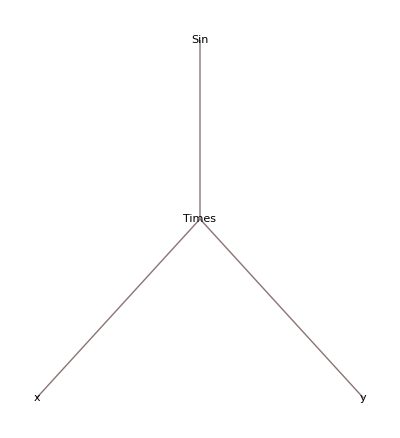

```mathematica
TreeForm[Sin[x y]]
```

```mathematica
Part[Plot[x,{x,0,1},PlotRange->All],2]
```

{AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→{None,None},AxesOrigin→{0,0},Method→{},PlotRange→{All,All},PlotRangeClipping→True,PlotRangePadding→{Automatic,Automatic}}

```mathematica
Outer[NIntegrate[Exp[-x^2],{x,0,#1},Method->#2,EvaluationMonitor:> Print["x"]]&,Xmax,method]
```

x

x

x

«325 more identical outputs»

{{0.886227,0.886227},{0.886227,0.886227}}

```mathematica
sh[1k ,h h0,H h0,x3 h0]/.{r1->1,r2->1,k->2Pi,h->1,x3->1.0+10^-1,H->8}
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

Indeterminate

```mathematica
sh[1k ,h h0,H h0,x3 h0]
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

Indeterminate

```mathematica
k
```

0

```mathematica
NIntegrate[BesselJ[0,x]Sinh[x]Sinh[x]/Sinh[2x],{x,0,Infinity}]//AbsoluteTiming
```

{0.53037,0.200369}

```mathematica
j0x2a1Nh[]
```

```mathematica
j1xshNhNearh[1,0,1,1,4]//AbsoluteTiming
```

NIntegrate::nconv: 振荡积分可能不是收敛的.

{2.30064,NIntegrate[(2 π) BesselJ[1,√(1^2+0^2) 2 π x] (2 π) x sh[x (2 π),1 1,4 1,1 1],{x,0,∞},Method→ExtrapolatingOscillatory]}

```mathematica
j1xshNh[r,0,1,1,4]//AbsoluteTiming
```

NIntegrate::inumr: 在以 {{∞, 0.}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r^2\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x]\ Sinh[2999999\ π\ x/500000] 得到非数值.

{1.04474,NIntegrate[(2 π) BesselJ[1,√(r^2+0^2) 2 π x] (2 π) x sh[x (2 π),1 1,4 1,1000001/1000000],{x,0,∞},Method→ExtrapolatingOscillatory]}